```mathematica
(*To run this notebook, select all cells, and shift enter to run.*)
```

```mathematica
fieldlines={{{{{2.2309683075566284,-0.01230766729639836},{2.231435513142097,0.},{2.2309683075566284,0.01230766729639836},{2.229571987266622,0.024579856405981454},193,{0.03635027791740902,0.8131286471593415},{0.02423453779337793,0.8152029565947085},{0.01211777458888166,0.8172704103236254},1},248,{1}}}, {{{, , , , }}}};
```

```mathematica
Dimensions[fieldlines](*should be {250, 201}*)
```

{250,201}

```mathematica
plotlist={};
AbsoluteTiming[
Monitor[
For[t=1,t<Length[fieldlines]+1,t++,
plotlist=Append[plotlist,ListLinePlot[fieldlines[[t]],ColorFunction->Blue,AspectRatio->1/3,PlotRange->All,AxesLabel->{"X","Z"}]]
]
,ProgressIndicator[t,{1,doreps+1}]]
]
```

{5.06353,Null}

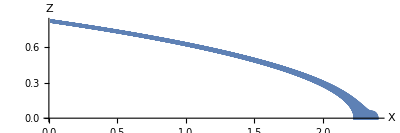

```mathematica
Show[plotlist,PlotRange->All]
```

```mathematica
(*Above is a plot of all the field lines.*)
```

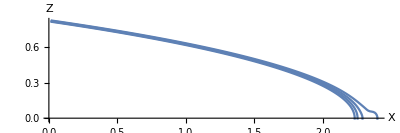

```mathematica
Show[plotlist[[1]],plotlist[[84]],plotlist[[167]],plotlist[[250]],PlotRange->All,BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

```mathematica
(*Above is a sample plot of the field lines while they retain relative accuracy. You can use the following command to see field lines i, j, and k, where 1 ≤ i ≤ 250, 1 ≤ j ≤ 250, and 1 ≤ k ≤ 250: Show[plotlist[[i]],plotlist[[j]],plotlist[[k]],PlotRange->All,BaseStyle->{FontWeight->"Bold",FontSize->12}].

 Below is a manipulate dynamic of the field lines.*)
```

```mathematica
Manipulate[plotlist[[i]],{i,1,250,1}]
```